```mathematica
nMatrix= Import[NotebookDirectory[]<>"n.mat"]⟦1⟧;
Dimensions@nMatrix;
nMatrix=Transpose[nMatrix,{1,5,4,2,3}];
{frames,X,Y,Z}=Dimensions[nMatrix]⟦;;-2⟧
θMatrix=ArcTan[nMatrix⟦;;,;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,;;,2⟧];
```

{20,12,12,8}

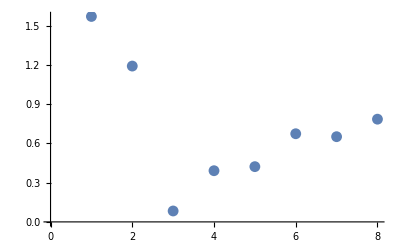

```mathematica
ArcTan@@#&/@nMatrix⟦-1,2,2,;;,{1,2}⟧//ListPlot
```

```mathematica
Dimensions@nMatrix
```

{20,12,12,8,3}

```mathematica
Manipulate[ListVectorPlot[nMatrix⟦frame,;;,;;,zz,;;2⟧,VectorStyle->Arrowheads[0],VectorPoints->All, VectorScale->{.1}],{frame,1,frames,1},{zz,1,Z,1}]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

Visualization`Core`ListVectorPlot::vfldata: {« 1 »} ⟦ 8, 1 ;; All, 1 ;; All, Null, 1 ;; 2 ⟧ is not a valid vector field dataset or a valid list of datasets.

Part::pkspec1: The expression Null cannot be used as a part specification.

Visualization`Core`ListVectorPlot::vfldata: {« 1 »} ⟦ 20, 1 ;; All, 1 ;; All, Null, 1 ;; 2 ⟧ is not a valid vector field dataset or a valid list of datasets.

Part::partd: Part specification {{« 1 »}, « 18 », {{{{0., 1., 0.}, {-0.583959, -0.591251, -0.556251}, {0.699205, 0.707481, -0.102874}, {0.724084, 0.684405, 0.0853904}, {0.681553, 0.706019, 0.192412}, {0.697568, 0.713011, -0.0708127}, {0.67977, 0.71581, 0.159776}, {0.707107, 0.707107, 0.}}, « 11 »}, « 11 »}} is longer than depth of object.

Visualization`Core`ListVectorPlot::vfldata: {« 1 »} ⟦ 20, 1 ;; All, 1 ;; All, 0, 1 ;; 2 ⟧ is not a valid vector field dataset or a valid list of datasets.

```mathematica
nMatrix
```

{1}
 |  |  |  |

```mathematica
SingleBrfMatrix[θ_,Δϕ_]:={{Cos[θ]^2+ⅇ^(-ⅈ Δϕ) Sin[θ]^2,(1-ⅇ^(-ⅈ Δϕ)) Cos[θ] Sin[θ]},{(1-ⅇ^(-ⅈ Δϕ)) Cos[θ] Sin[θ],ⅇ^(-ⅈ Δϕ) Cos[θ]^2+Sin[θ]^2}}
JonesMatrices=Table[Map[Apply[Dot,Reverse[#]]&,Map[SingleBrfMatrix[#,0.6]&,θMatrix⟦frame⟧,{3}],{2}],{frame,Length@θMatrix}];
```

```mathematica
Manipulate[ArrayPlot[Abs@Map[Flatten[#.{{Cos[γ]},{Sin[γ]}}]⟦1⟧&,JonesMatrices⟦frame⟧,{2}],ColorFunction->GrayLevel,ColorFunctionScaling->False],{frame,1,frames,1},{γ,0,π/2}]
```